```mathematica
(*Leah Dougherty
ChE 272 HW 5: Biofermenter*)
```

```mathematica
V=50;
ak=2.5;
F=5;
gp=F;
gd=ak;
gm[s]=(V*s+ak+F-1)/F;
kc=0.5;
tauI=3;
```

```mathematica
gc=kc*(tauI*s+1)/(tauI*s);
```

```mathematica
(*For a system without disturbances*)
```

(0.833333 (1+3 s))/(s^2 (1+(0.166667 (1+3 s) (29+50 s))/s))

0.833333 (0.206897-0.161526 ⅇ^(-0.660726 t)-0.045371 ⅇ^(-0.292607 t))

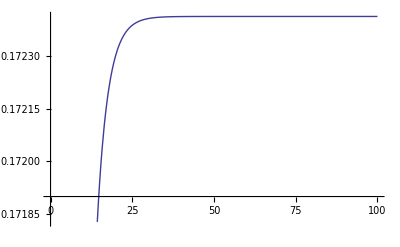

```mathematica
sConcentration=(gc*gp/(1+gc*gp*gm[s]))*(1/s)
tConcentration=InverseLaplaceTransform[sConcentration,s,t]
Plot[tConcentration, {t,0,100}]
```

```mathematica
(*For a system with disturbances*)
```

```mathematica
(*Co=Sparger Oxygen Supply Concentration; assumed to be constant*)
```

12.5/(s (1+(0.166667 (1+3 s) (6.5+50 s))/s))+(0.833333 (1+3 s))/(s^2 (1+(0.166667 (1+3 s) (6.5+50 s))/s))

0.769231-1.82139 ⅇ^(-0.393098 t)+1.05216 ⅇ^(-0.110235 t)

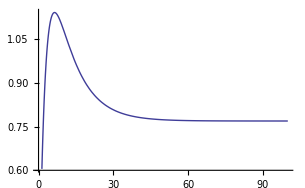

```mathematica
Co=5;
sConcentration2=(gc*gp/(1+gc*gp*gm[s]))*(1/s)+(gd/(1+gc*gp*gm[s]))*(Co/s)
tConcentration2=InverseLaplaceTransform[sConcentration2,s,t]
Plot[tConcentration2, {t,0,100}]
```